```mathematica
Remove["Global`*"]
```

Define the expectation for a time-dependent Ornstein-Uhlenbeck process

```mathematica
Expand[( EX*Exp[(1-f)*T]-(X0)-(1-f)*Integrate[μ[t]*Exp[(1-f)*t],{t,0,T}])^2 == (1-f)^2*Integrate[Exp[2*(1-f)*t]*σ[t]^2,{t,0,T}]]
```

ⅇ^(2 (1-f) T) EX^2-2 ⅇ^((1-f) T) EX X0+X0^2-2 ⅇ^((1-f) T) EX ∫_0^T ⅇ^((1-f) t) μ[t]ⅆt+2 ⅇ^((1-f) T) EX f ∫_0^T ⅇ^((1-f) t) μ[t]ⅆt+2 X0 ∫_0^T ⅇ^((1-f) t) μ[t]ⅆt-2 f X0 ∫_0^T ⅇ^((1-f) t) μ[t]ⅆt+(∫_0^T ⅇ^((1-f) t) μ[t]ⅆt)^2-2 f (∫_0^T ⅇ^((1-f) t) μ[t]ⅆt)^2+f^2 (∫_0^T ⅇ^((1-f) t) μ[t]ⅆt)^2==∫_0^T ⅇ^(2 (1-f) t) σ[t]^2ⅆt-2 f ∫_0^T ⅇ^(2 (1-f) t) σ[t]^2ⅆt+f^2 ∫_0^T ⅇ^(2 (1-f) t) σ[t]^2ⅆt

```mathematica
ESquareXFull= (∫_0^T ⅇ^(2 (1-f) t) σ[t]^2 ⅆt-2 f ∫_0^T ⅇ^(2 (1-f) t) σ[t]^2 ⅆt+f^2 ∫_0^T ⅇ^(2 (1-f) t) σ[t]^2 ⅆt- (-2 ⅇ^((1-f) T) EX X0+X0^2-2 ⅇ^((1-f) T) EX ∫_0^T ⅇ^((1-f) t) μ[t]ⅆt+2 ⅇ^((1-f) T) EX f ∫_0^T ⅇ^((1-f) t) μ[t]ⅆt+2 X0 ∫_0^T ⅇ^((1-f) t) μ[t]ⅆt-2 f X0 ∫_0^T ⅇ^((1-f) t) μ[t]ⅆt+(∫_0^T ⅇ^((1-f) t) μ[t]ⅆt)^2-2 f (∫_0^T ⅇ^((1-f) t) μ[t]ⅆt)^2+f^2 (∫_0^T ⅇ^((1-f) t) μ[t]ⅆt)^2))/ⅇ^(2 (1-f) T)
```

ⅇ^(-2 (1-f) T) (2 ⅇ^((1-f) T) EX X0-X0^2+2 ⅇ^((1-f) T) EX ∫_0^T ⅇ^((1-f) t) μ[t]ⅆt-2 ⅇ^((1-f) T) EX f ∫_0^T ⅇ^((1-f) t) μ[t]ⅆt-2 X0 ∫_0^T ⅇ^((1-f) t) μ[t]ⅆt+2 f X0 ∫_0^T ⅇ^((1-f) t) μ[t]ⅆt-(∫_0^T ⅇ^((1-f) t) μ[t]ⅆt)^2+2 f (∫_0^T ⅇ^((1-f) t) μ[t]ⅆt)^2-f^2 (∫_0^T ⅇ^((1-f) t) μ[t]ⅆt)^2+∫_0^T ⅇ^(2 (1-f) t) σ[t]^2ⅆt-2 f ∫_0^T ⅇ^(2 (1-f) t) σ[t]^2ⅆt+f^2 ∫_0^T ⅇ^(2 (1-f) t) σ[t]^2ⅆt)

```mathematica
EXsol =  (X0)*Exp[-(1-f)*T]+(1-f)*Exp[-(1-f)*T]*Integrate[Exp[(1-f)*t]*μ[t],{t,0,T}]
```

ⅇ^((-1+f) T) X0+ⅇ^((-1+f) T) (1-f) ∫_0^T ⅇ^((1-f) t) μ[t]ⅆt

```mathematica
ESquareX=FullSimplify[ESquareXFull/.EX ->EXsol]
```

ⅇ^(2 (-1+f) T) ((X0-(-1+f) ∫_0^T ⅇ^(t-f t) μ[t]ⅆt)^2+(-1+f)^2 ∫_0^T ⅇ^(-2 (-1+f) t) σ[t]^2ⅆt)

```mathematica
SquareEX =FullSimplify[ ( EXsol)^2]
```

ⅇ^(2 (-1+f) T) (X0-(-1+f) ∫_0^T ⅇ^(t-f t) μ[t]ⅆt)^2

```mathematica
ESquareX
SquareEX
```

ⅇ^(2 (-1+f) T) ((X0-(-1+f) ∫_0^T ⅇ^(t-f t) μ[t]ⅆt)^2+(-1+f)^2 ∫_0^T ⅇ^(-2 (-1+f) t) σ[t]^2ⅆt)

ⅇ^(2 (-1+f) T) (X0-(-1+f) ∫_0^T ⅇ^(t-f t) μ[t]ⅆt)^2

```mathematica
VarXFull=ESquareX-SquareEX
```

-ⅇ^(2 (-1+f) T) (X0-(-1+f) ∫_0^T ⅇ^(t-f t) μ[t]ⅆt)^2+ⅇ^(2 (-1+f) T) ((X0-(-1+f) ∫_0^T ⅇ^(t-f t) μ[t]ⅆt)^2+(-1+f)^2 ∫_0^T ⅇ^(-2 (-1+f) t) σ[t]^2ⅆt)

```mathematica
VarX = FullSimplify[VarXFull]
```

ⅇ^(2 (-1+f) T) (-1+f)^2 ∫_0^T ⅇ^(-2 (-1+f) t) σ[t]^2ⅆt

ⅇ^((-1+f) T) (X0-μ0)+ⅇ^((-1+f) T) (1-f) ((5-5 ⅇ^(T-f T))/(1-f)+(1-ⅇ^(T-f T) (Cos[T]+(-1+f) Sin[T]))/(2+(-2+f) f))

(ⅇ^(2 (-1+f) T) (-1+ⅇ^(-2 (-1+f) T)) (-1+f)^2)/(2-2 f)

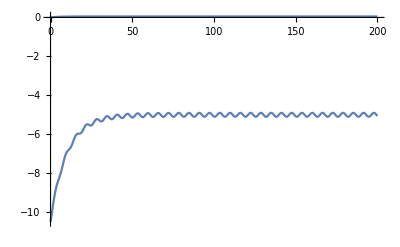

```mathematica
EXspecific = EXsol/.{μ[t]->-5+Sin[t],σ[t]->1}
VarXSpecific=VarX/.{μ[t]->-5+Sin[t],σ[t]->1}
Plot[{EXspecific,VarXSpecific}/.{f->0.9,X0->-10,μ0->0.5},{T,0,200}]
```

{-10.5 ⅇ^(-0.1 T)+0.1 ⅇ^(-0.1 T) (10.9901-10. ⅇ^(0.1 T)+ⅇ^(0.1 T) (-0.990099 Cos[T]+(0.0990099+1.73472×10^-18 ⅈ) Sin[T])),0.04 ⅇ^(-0.2 T) (-2.47525+ⅇ^(0.2 T) (2.5-0.0247525 Cos[2. T]-0.247525 Sin[2. T]))}

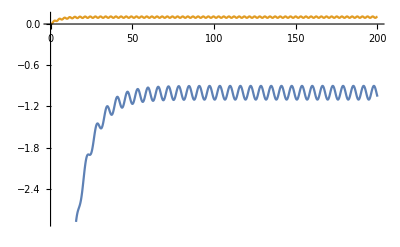

```mathematica
ExpVar = {EXspecific = EXsol,VarXSpecific=VarXFull}/.{μ[t]->-1+Sin[t],σ[t]->2*Sin[t],f->0.9,X0->-10,μ0->0.5}
Plot[ExpVar,{T,0,200}]
```

```mathematica
EXsol/.{μ[t]->-1+Sin[t],σ[t]->2*Sin[t],f->0.5,X0->-10,μ0->0.5}
```

-10.5 ⅇ^(-0.5 T)+0.5 ⅇ^(-0.5 T) (2.8-2. ⅇ^(0.5 T)+ⅇ^(0.5 T) (-0.8 Cos[T]+0.4 Sin[T]))

```mathematica
FullSimplify[%]
```

-1.-9.1 ⅇ^(-0.5 T)-0.4 Cos[T]+0.2 Sin[T]